```mathematica
ClearAll["`*"]
L=1;m^2=-2;
SetDirectory[NotebookDirectory[]];
```

## eigen equation

```mathematica
vars={t,r,x,y};xa[μ_]:=vars⟦μ⟧;dim=Length[vars];
f[r_]:=1-(1+mu^2/(4 zh^2)) (1-r^2)^3+mu^2/(4 zh^2)(1-r^2)^4;
ds^2=zh^2/((1-r^2)^2)(-f[r] Dt[t]^2+(4 r^2 Dt[r]^2)/(zh^2 f[r])+Dt[x]^2+Dt[y]^2);
coematrix=Coefficient[ds^2,Dt[vars]⊗Dt[vars]];
metric=1/2 Simplify[coematrix+DiagonalMatrix[Diagonal[coematrix]]];
gbb[μ_,ν_]:=metric⟦μ,ν⟧;
invmetric=Simplify[Inverse[metric]];
gaa[μ_,ν_]:=invmetric⟦μ,ν⟧;
g=Simplify[Det[metric]];
(*Γabb[λ_,μ_,ν_]:=Simplify[∑_(σ=1)^dim 1/2 gaa[λ,σ] (-∂_xa[σ] gbb[μ,ν]+∂_xa[μ] gbb[ν,σ]+∂_xa[ν] gbb[σ,μ])];*)
(*ansatz for scalar field*)
Φ=(1-r^2)/zh ϕ[r];
A={mu/(√e) r^2,0,0,0};
Ab[μ_]:=A⟦μ⟧;Aa[ν_]:=∑_(σ=1)^dim gaa[σ,ν] Ab[σ];
DΦb[μ_]:=D[Φ, xa[μ]]-ⅈ Ab[μ]Φ;
scalar=Simplify[1/(√-g)∑_(μ=1)^dim (D[#, xa[μ]]-ⅈ Ab[μ]#&[√-g ∑_(ν=1)^dim gaa[μ,ν] DΦb[ν]])-m^2 Φ];
nonfactor[eqs_]:=Block[{First,Last,FactorList},SetAttributes[{First,Last,FactorList},Listable];Simplify[First[Last[FactorList[eqs]]]]];
eqs=Simplify[nonfactor[scalar]];
jacobi=Simplify[Coefficient[(eqs/.{Derivative[i_][h_][r]->Subscript[dr, i] h[r],h_[r]->eye h[r]}),ϕ[r]]];
Simplify[Collect[jacobi,zh]]
subeqs=eqs/.{Derivative[i_][h_][r]:>D[(Series[h[r],{r,0,3}]), {r,i}],h_[r]:>Series[h[r],{r,0,3}]};
```

4 e eye mu^4 r (-1+r^2)^4 (-1+2 r^2)+e mu^4 (-1+r^2)^5 (-1+7 r^2) dr_1+e mu^4 r (-1+r^2)^6 dr_2+16 e (3-3 r^2+r^4) zh^4 (4 eye r (-1+r^2)+(3-9 r^2+5 r^4) dr_1+r (3-3 r^2+r^4) dr_2)+8 mu^2 zh^2 (8 eye r^3+2 e eye r (-1+r^2) (-4+12 r^2-10 r^4+3 r^6)+3 e (-1+r^2)^2 (-1+6 r^2-6 r^4+2 r^6) dr_1+e r (-1+r^2)^3 (3-3 r^2+r^4) dr_2)

```mathematica
Simplify[SeriesCoefficient[subeqs,{r,0,0}]]
Simplify[SeriesCoefficient[eqs,{r,0,0}]]
X=Simplify[Coefficient[jacobi,zh^4]]
Y=Simplify[Coefficient[jacobi,zh^2]]
Z=Simplify[jacobi/.zh->0]
```

e (mu^2-12 zh^2)^2 ϕ'[0]

e (mu^2-12 zh^2)^2 ϕ'[0]

16 e (3-3 r^2+r^4) (4 eye r (-1+r^2)+(3-9 r^2+5 r^4) dr_1+r (3-3 r^2+r^4) dr_2)

8 mu^2 (8 eye r^3+2 e eye r (4-16 r^2+22 r^4-13 r^6+3 r^8)+3 e (-1+r^2)^2 (-1+6 r^2-6 r^4+2 r^6) dr_1+e r (-1+r^2)^3 (3-3 r^2+r^4) dr_2)

e mu^4 (-1+r^2)^4 (4 eye r (-1+2 r^2)+(1-8 r^2+7 r^4) dr_1+r (-1+r^2)^2 dr_2)

## eigenvalue

```mathematica
Nr=56;Lr=1;mu=5.6;e=1;
(*Chebshev谱求导矩阵生成函数*)
chebp[n_]:=Table[Cos[(i π)/(n-1.0)],{i,0,n-1}];
cheb[n_,l_]:=Module[{x,c,sdm},x=chebp[n];c=Table[If[i==1||i==n,2.0,1.0],{i,1,n}];sdm=2/l Table[If[i≠j,c[[i]]/c[[j]](-1)^(i+j)/(x[[i]]-x[[j]]),0],{i,1,n},{j,1,n}];sdm-=DiagonalMatrix[Total[sdm,{2}]]];
Eye=IdentityMatrix[Nr];Zero=ConstantArray[0,{Nr,Nr}];
gridr=0.5(chebp[Nr]+1);
dr=cheb[Nr,Lr];drs[1]=dr;drs[2]=dr.dr;
{Xm,Ym,Zm}={X,Y,Z}/.{Subscript[dr, i_]->drs[i],eye->Eye,r-> gridr};
Xm⟦1⟧=Zero⟦1⟧;Xm⟦-1⟧=Zero⟦-1⟧;
Ym⟦1⟧=Zero⟦1⟧;Ym⟦-1⟧=Zero⟦-1⟧;
Zm⟦1⟧=dr⟦1⟧;Zm⟦-1⟧=dr⟦-1⟧;
left=ArrayFlatten[{{-Ym,-Zm},{Eye,Zero}}];
right=ArrayFlatten[{{Xm,Zero},{Zero,Eye}}];
EV=Chop[Eigenvalues[{left,right}]]
EVmax=Max[Abs[DeleteCases[DeleteCases[EV,∞],ComplexInfinity]]]
(√e)/mu(zh/(4π)(3- mu^2/(4 zh^2)))/.zh->√EVmax
```

{ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,27.1885,2.74898,2.61445,2.61336,2.61333,2.61333-0.000178001 ⅈ,2.61333+0.000178001 ⅈ,2.61323,2.61286,2.61193,2.61184-0.000642426 ⅈ,2.61184+0.000642426 ⅈ,2.61013,2.60685+0.000493095 ⅈ,2.60685-0.000493095 ⅈ,2.60521,2.60209,2.59481-0.000834444 ⅈ,2.59481+0.000834444 ⅈ,2.58865,2.58461,2.57082-0.00106775 ⅈ,2.57082+0.00106775 ⅈ,2.55794,2.55286,2.52993+0.000621026 ⅈ,2.52993-0.000621026 ⅈ,2.50791,2.50168,2.46911,2.46529,2.43387,2.42623,2.38182,2.37476,2.33192,2.32267,2.26498,2.25497,2.19938,2.18873,2.11675,2.10467,2.03538,2.02413,1.93735,1.92474,1.84147,1.83084,1.72951,1.71858,1.62213,1.61307,1.49866,1.49221,1.3856,1.37665,1.25355+0.00174769 ⅈ,1.25355-0.00174769 ⅈ,1.143,1.12943,1.0125,1.00533,0.904924,0.883492,0.782075,0.764781,0.682173,0.652337,0.57227,0.545888,0.485092,0.448544,0.392676,0.359861,0.321715,0.282052,0.249497,0.214482,0.196238,0.15822,0.144493,0.112164,0.108222,0.0765437,0.0746335,0.0526405,0.0493875,0.0337162,0.0300471,0.0219619,0.017055,0.0126886,0.00884827,0.00747226,0.00413134,0.00371249,0.00187984,0.00166763,0.000697602,0.00055879,0.000241351,0.000147884,0.0000278346,3.2564×10^-6,1.81193×10^-7,2.56655×10^-9,0}

27.1885

0.200922

## data

### data1

```mathematica
Clear[e];
Nr=65;Lr=1;mu=5.6;etbcs={};
(*Chebshev谱求导矩阵生成函数*)
chebp[n_]:=Table[Cos[(i π)/(n-1.0)],{i,0,n-1}];
cheb[n_,l_]:=Module[{x,c,sdm},x=chebp[n];c=Table[If[i==1||i==n,2.0,1.0],{i,1,n}];sdm=2/l Table[If[i≠j,c[[i]]/c[[j]](-1)^(i+j)/(x[[i]]-x[[j]]),0],{i,1,n},{j,1,n}];sdm-=DiagonalMatrix[Total[sdm,{2}]]];
Eye=IdentityMatrix[Nr];Zero=ConstantArray[0,{Nr,Nr}];
gridr=0.5(chebp[Nr]+1);
dr=cheb[Nr,Lr];drs[1]=dr;drs[2]=dr.dr;
Do[{Xm,Ym,Zm}={X,Y,Z}/.{Subscript[dr, i_]->drs[i],eye->Eye,r-> gridr};
Xm⟦1⟧=Zero⟦1⟧;Xm⟦-1⟧=Zero⟦-1⟧;
Ym⟦1⟧=Zero⟦1⟧;Ym⟦-1⟧=Zero⟦-1⟧;
Zm⟦1⟧=Eye⟦1⟧;Zm⟦-1⟧=dr⟦-1⟧;
left=ArrayFlatten[{{-Ym,-Zm},{Eye,Zero}}];
right=ArrayFlatten[{{Xm,Zero},{Zero,Eye}}];
EV=Chop[Eigenvalues[{left,right}]];
EVmax=Max[Abs[DeleteCases[DeleteCases[EV,Infinity],ComplexInfinity]]];
AppendTo[etbcs,{e,(√e)/mu(zh/(4π)(3- mu^2/(4 zh^2)))/.zh->√EVmax}];,{e,10.^-4,1,0.05}]
```

{{0.0001,0.0587412},{0.0501,0.0557256},{0.1001,0.0528532},{0.1501,0.0501203},{0.2001,0.0475228},{0.2501,0.0450567},{0.3001,0.0427175},{0.3501,0.0405011},{0.4001,0.0384029},{0.4501,0.0364183},{0.5001,0.0345428},{0.5501,0.0327718},{0.6001,0.0311006},{0.6501,0.0295246},{0.7001,0.0280394},{0.7501,0.0266402},{0.8001,0.0253229},{0.8501,0.024083},{0.9001,0.0229163},{0.9501,0.0218187}}

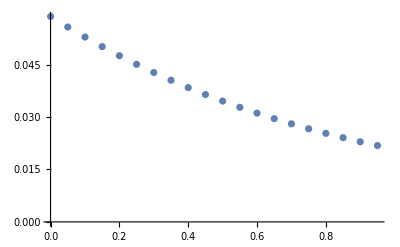

```mathematica
etbcs
ListPlot[etbcs,PlotRange->All]
```

### data2

```mathematica
Clear[e];
Nr=66;Lr=1;mu=5.6;etbec={};
(*Chebshev谱求导矩阵生成函数*)
chebp[n_]:=Table[Cos[(i π)/(n-1.0)],{i,0,n-1}];
cheb[n_,l_]:=Module[{x,c,sdm},x=chebp[n];c=Table[If[i==1||i==n,2.0,1.0],{i,1,n}];sdm=2/l Table[If[i≠j,c[[i]]/c[[j]](-1)^(i+j)/(x[[i]]-x[[j]]),0],{i,1,n},{j,1,n}];sdm-=DiagonalMatrix[Total[sdm,{2}]]];
Eye=IdentityMatrix[Nr];Zero=ConstantArray[0,{Nr,Nr}];
gridr=0.5(chebp[Nr]+1);
dr=cheb[Nr,Lr];drs[1]=dr;drs[2]=dr.dr;
Do[{Xm,Ym,Zm}={X,Y,Z}/.{Subscript[dr, i_]->drs[i],eye->Eye,r-> gridr};
Xm⟦1⟧=Zero⟦1⟧;Xm⟦-1⟧=Zero⟦-1⟧;
Ym⟦1⟧=Zero⟦1⟧;Ym⟦-1⟧=Zero⟦-1⟧;
Zm⟦1⟧=dr⟦1⟧;Zm⟦-1⟧=dr⟦-1⟧;
left=ArrayFlatten[{{-Ym,-Zm},{Eye,Zero}}];
right=ArrayFlatten[{{Xm,Zero},{Zero,Eye}}];
EV=Chop[Eigenvalues[{left,right}]];
EVmax=Max[Abs[DeleteCases[DeleteCases[EV,Infinity],ComplexInfinity]]];
AppendTo[etbec,{e,(√e)/mu(zh/(4π)(3- mu^2/(4 zh^2)))/.zh->√EVmax}];,{e,10.^-4,1,0.05}]
```

{{0.0001,0.213069},{0.0501,0.212417},{0.1001,0.211769},{0.1501,0.211127},{0.2001,0.210489},{0.2501,0.209856},{0.3001,0.209228},{0.3501,0.208605},{0.4001,0.207986},{0.4501,0.207372},{0.5001,0.206763},{0.5501,0.206159},{0.6001,0.205559},{0.6501,0.204963},{0.7001,0.204372},{0.7501,0.203786},{0.8001,0.203204},{0.8501,0.202627},{0.9001,0.202054},{0.9501,0.201485}}

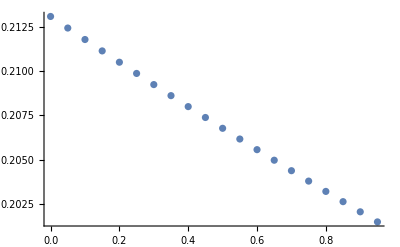

```mathematica
etbec
ListPlot[etbec,PlotRange->All]
```

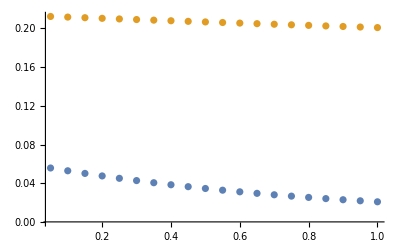

```mathematica
ListPlot[{etbcs,etbec},PlotRange->All]
```